V19 : I want to check whether I can change the normalization of γ by evaluating χ_1^1 on the next time step

# Graphics

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

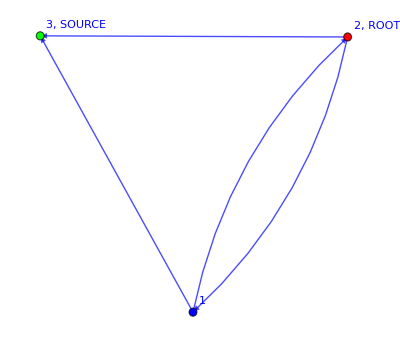

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

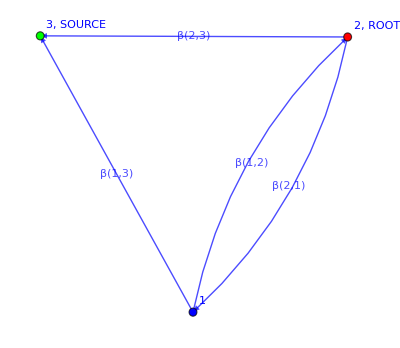

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Graph[EdgeList[g],EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,ROOT,PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,SOURCE,Name},VertexStyle→{PropertyValue[]⟦1⟧→RGBColor[1, 0, 0],PropertyValue[]⟦1⟧→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

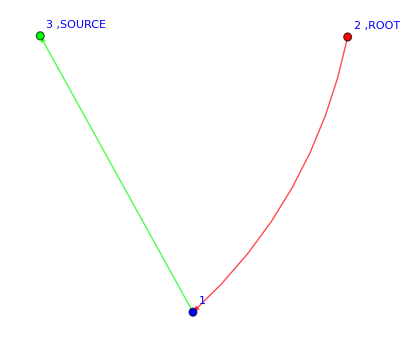

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

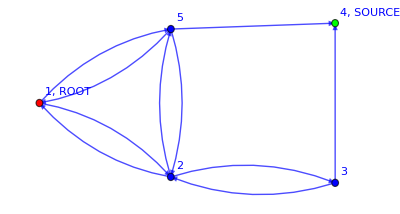

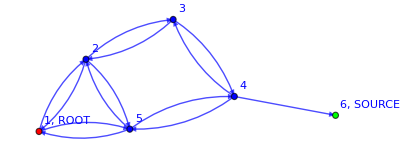
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Field Theory tools

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

#### Test

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Vertex rules and VertexAssignment[]

The vertices are where the interaction takes place in the field theory.

```mathematica
Clear[V];
V[1.]:=1.;
V[1]:=1;
(*V[0]:=0;*)
V'[a_]:=1
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{},"sourceBC"->1};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locSource,action,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

(*LERW*)
If[OptionValue["system"]=="LERW",
If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
action = Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ]],{x,Length[locVertices]}];
action*=V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[i, s]])];(*This is the BC*)
Return[action]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}])] ],{x,Length[locVertices]}]
]]
]
```

### Usage example of VertexAssignment[]

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW"]
```

(1+χ[4,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

```mathematica
VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{1}]
```

(1+χ[4,i_s]) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

## δrules

```mathematica
ClearAll[Σδrule]
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[l, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[jj, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[ll, _]]):>1};
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

δ[a,a]

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

m

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## Operator “vertices” rules

```mathematica
Clear[Op];
Op[1]:=1;
Op[0]:=0;
Op'[_]:=1
```

## FieldsNamesGenerator[]

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

#### Test

```mathematica
fields={ϕ,χ};
FieldsNamesGenerator[fields]//AbsoluteTiming
FieldsNamesGenerator[fields]//AbsoluteTiming
```

{0.0000616,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

{3.1×10^-6,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

## WickContractionBlock[]

```mathematica
(*IT SHOULD BE WORKING WITH 4 FIELDS TOO!!!!!*)
```

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->{χ}, "endTime"->1,"#vertices"->10};

WickContractionBlock[A_ +B_,OptionsPattern[]]:=WickContractionBlock[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[Op[A_ +B_]*C_,OptionsPattern[]]:=WickContractionBlock[Op[A]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[Op[B]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,jj,l,timeIndex},

z=V[A]B;

(*
If[OptionValue["print"],
Print["###################  Partition Function  ##################"];
];*)

(* Updated version with FieldsNamesGenarator
locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)
*)

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[jj=1,jj<=OptionValue["#vertices"],jj++,

(*First contribution*)
zTemp1=z//.locFields[[l]][jj,a_]->0//.starFields[[l]][jj,a_]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
(*Print["First contribution: ",zTemp1];*)
];

(*Second contribution*)
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1=D[zTemp1,κ]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+κ *deltaStarFields[[l]][jj,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,κ]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;


If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Second contribution: ",zTemp1];*)
];


(*THIRD contribution*)
zTemp1=z/. locFields[[l]][jj,a_]->locFields[[l]][jj,a]+κ *deltaFields[[l]][jj,a];
If[zTemp1-z=!=0,
zTemp1=1/2 D[zTemp1,{κ,2}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][jj,a_]->starFields[[l]][jj,a]+κ *deltaStarFields[[l]][jj,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,2}]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];
zTemp2=zTemp1//.deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_]*deltaFields[[l]][jj,a_]*deltaStarFields[[l]][jj,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b]*δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][jj,a_]->0/.deltaStarFields[[l]][jj,b_]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Third contribution: ",zTemp1];*)
];

z=contributions;


(*Print["Overall contributions: ",contributions];
Print["################################"];*)

contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

### WickContractionBlock[] quartic term test

Simple

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
Z=VertexAssignment[g,"system"->"LERW"];
WickContractionBlock[Z ,"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]/.n->-1
WickContractionBlock[Z Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]],"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]/.n->-1
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))

-1+(2 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))

```mathematica
(*IT SEEMS TO BE WORKING EVEN WITH 4 FIELDS!!!!*)
```

```mathematica
WickContractionBlock[V[ 1+Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]]] Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]],"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]
```

3 n

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source][[1]];
g;
Z=VertexAssignment[g]
WickContractionBlock[Z,"fields"->{χ}, "endTime"->1]/.n->-1
```

V[1+χ_(3,i_s)] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,3))+(β_(1,3) χ_(1,i_1) (χ^*)_(3,i_1))/(β_(1,2)+β_(1,3))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,2) χ_(2,i_2) (χ^*)_(2,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))]

1.-(1. β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,2)+β_(2,3)))-(1. β_(2,2))/(β_(2,1)+β_(2,2)+β_(2,3))

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

## ExpectationValueBlock[]

```mathematica
Clear[ExpectationValueBlock];
Options[ExpectationValueBlock]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1},"externalδ"->True,"nχ"->-1,"nα"->0};

ExpectationValueBlock[Z_,OptionsPattern[]]:=Block[{Nvertices,z,terms,graphs={},i},

Nvertices=Length[VertexList@OptionValue["graph"]];

If[OptionValue["operator"]===1,
(*True*)z=WickContractionBlock[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
],
(*False*)z=WickContractionBlock[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
]/WickContractionBlock[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices]
];

If[OptionValue["externalδ"],
z=z//.δruleExternal];
z=z/.n->OptionValue["nχ"];
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

### ExpectationValue[] vs ExpectationValueBlock[] speed test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=myFavoriteGraph;
Z=VertexAssignment[g];
ExpectationValue[Z]//AbsoluteTiming
ExpectationValueBlock[Z,"graph"->g]//AbsoluteTiming
```

{0.0649989,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

{0.0150432,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

It  does  seem  to  be  faster  indeed

## LERWtransitionProb[]

This function computes the transition probability as

```mathematica
Clear[LERWtransitionProb];
Options[LERWtransitionProb]={"draw"->False,"print"->False};

LERWtransitionProb[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j},
locBC={{ϕ[locSource]==1},{locSource}};

For[i=1,i<=Length[path],i++,

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z*χs[path[[i,1]],1]];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

denominator=Z//FullSimplify;


(*Then we need to solve it again with updated BC at the current step*)

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];
(*Print[locBC]*);


Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]],"sourceBC"->denominator^-1];
Z=ExpectationValue[Z*χs[path[[i,2]],1] ];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

numerator=locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Z//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[numerator/.β[_,_]->1//FullSimplify];

prob*=numerator//FullSimplify;
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

LaplacianRW[-Graphics-,{{2,1},{1,3}}]

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

```mathematica
VertexAssignment[g,"excludedVertices"->{2,3}]
LERWtransitionProb[g,path1]
```

(1+χ[3,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3]))

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

Let’s try with another example, i.e. my favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
PathFinder[myFavoriteGraph]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}}

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

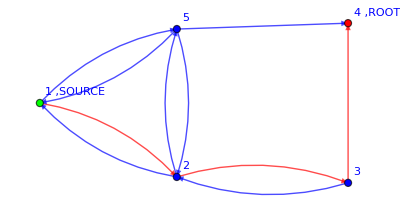

3/11

```mathematica
path2={{1,2},{2,3},{3,4}};
LaplacianRW[myFavoriteGraph,path2,"draw"->True]/.β[_,_]->1
```

```mathematica
LERWtransitionProb[myFavoriteGraph,path2]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

3/11

```mathematica
(*Correct!!!*)
```

## Znorm[]

```mathematica
Clear[Znorm];
Options[Znorm]={"graph"->g,"fieldsToExclude"->{ϕs,ψs},"theory"->"LERW","βrule"->{β[__]->1.}};

Znorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token,index},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)

For[index=1,index<=Length[OptionValue["fieldsToExclude"]],index++,
excludedVertices=excludedVertices/.OptionValue["fieldsToExclude"][[index]][a_,__]->a;
];
(*excludedVertices=excludedVertices/.ψs[a_,__]->a;
excludedVertices=excludedVertices/.ψs[a_,__]ψs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]ξs[a_,__]->a;*)

locZnorm=VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];

ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->FieldsNamesGenerator[{ϕ,χ}]]/.token->1
]
```

#### Test

```mathematica
g
```

-Graphics-

```mathematica
VertexAssignment[g]
```

V[1+χ_(4,i_s)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

```mathematica
ExpectationValue[%]
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
%/.β[__]->1
```

11/36

```mathematica
Znorm[+5/18 γ Subscript[R, 1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1}]
```

5/6

```mathematica
Znorm[+5/18 γ Subscript[R, 1,2,RGBColor[1, 0, 0]] ψs[2,Subscript[t, 2],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1}]
```

5/6

```mathematica
Znorm[+5/18 γ Subscript[R, 1,2,RGBColor[1, 0, 0]] ϕs[2,Subscript[t, 2],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}]
```

11/36

## DynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[DynamicLERWaction];
Options[DynamicLERWaction]={"sourceBC"->1};

DynamicLERWaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0 ,1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, -1]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
endTime=1;
DynamicLERWaction[myFavoriteGraph,endTime]
```

V[1+ϕ[1,t_1]] V[1+ϕ[2,t_1]] V[1+ϕ[3,t_1]] V[1+ϕ[5,t_1]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_1]] V[1+ψ[2,t_1]] V[1+ψ[3,t_1]] V[1+ψ[5,t_1]] V[1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])] V[1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])] V[1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2]]

## Evaluation of the DynamicLERWaction[]

Simple case

One time-slice

```mathematica
fields={χ,ϕ,ψ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g;

endTime=1;
Z=DynamicLERWaction[g,endTime];
```

###################  Partition Function  ##################

{{1},{-1/4,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

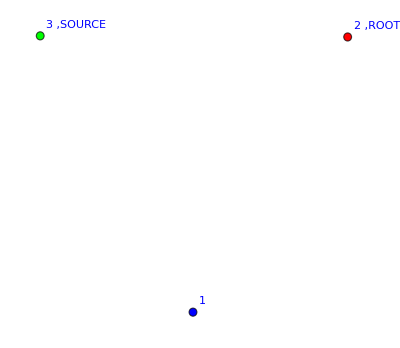

Weight 1

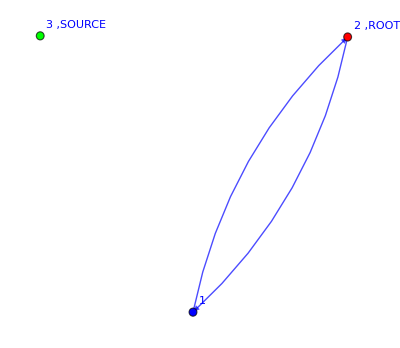

Weight   1
-(-)
  4

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z,"fields"->fields,"endTime"->endTime,"print"->False,"draw"->True,"graph"->g]
```

```mathematica
Z//.V[A_]->A;
GeneralizedExpectationValue[%,"draw"->True,"graph"->g]
```

Part::partw: Part 3 of {1,2} does not exist.

Part::partw: Part 3 of {2,1} does not exist.

{-Graphics-,-Graphics-}

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%]
%/.β[__]->1
```

$Aborted

$Aborted

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

```mathematica
WickContraction[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]]+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*IT IS WAAAAAY QUICKER!!!!!!!*)
```

```mathematica
ExpectationValue[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.V[_]->1
```

2+(2 β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(4 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Now let’s add an external field

With the generalized expectation value

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%* ϕs[2,Subscript[t, 1],Subscript[i, -1]]]
```

(β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
```

```mathematica
(*WARNING: VERY SLOW, DO NOT RUN THIS LINE*)GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Done with the enhanced WickContraction

###################  Partition Function  ##################

{{},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

-Graphics-

-Graphics-

-Graphics-

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

###################  Operator found  ##################

{{{1,3,RGBColor[0, 0, 1]},{1,3,RGBColor[1, 0, 0]},{2,1,RGBColor[1, 0, 0]}}}

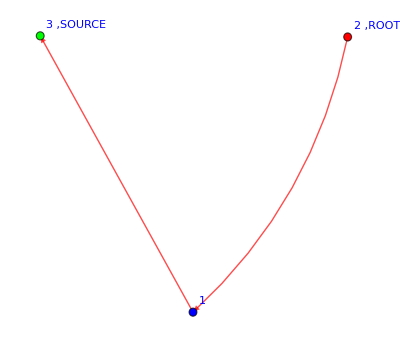

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
Z Op[ϕs[2,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[2,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

```mathematica
1+V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))/.f_[a_,Subscript[t, 3],b_]->f[a,b];
WickContraction[V[1]*%,"fields"->fields,"endTime"->0]
```

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

2+WickContraction[(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2),print→False,fields→{χ,ϕ,ψ},endTime→0]+WickContraction[-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])),print→False,fields→{χ,ϕ,ψ},endTime→0]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*expected*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]
```

```mathematica
(*Weight*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]//.f_[_,_,_]->1
```

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
(*THEY SEEM TO MATCH!!!!!!!!!*)
```

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ϕ[4,t_2,0]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_2,j_-1]] V[1+ψ[2,t_2,j_-1]] V[1+ψ[3,t_2,j_-1]] V[1+ψ[4,t_2,j_-1]] V[1+(R[1,2,RGBColor[0, 0, 1]] β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[0, 0, 1]] β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,2,RGBColor[1, 0, 0]] β[1,2] ϕ[1,t_1,k_1] ϕs[2,t_2,k_1] χs[2,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[1, 0, 0]] β[1,3] ϕ[1,t_1,k_1] ϕs[3,t_2,k_1] χs[3,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+ψ[1,t_1,j_-1] ψs[1,t_2,j_-1]] V[1+(R[2,1,RGBColor[0, 0, 1]] β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[0, 0, 1]] β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,1,RGBColor[1, 0, 0]] β[2,1] ϕ[2,t_1,k_2] ϕs[1,t_2,k_2] χs[1,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[1, 0, 0]] β[2,4] ϕ[2,t_1,k_2] ϕs[4,t_2,k_2] χs[4,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+ψ[2,t_1,j_-1] ψs[2,t_2,j_-1]] V[1+(R[3,1,RGBColor[0, 0, 1]] β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[0, 0, 1]] β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,1,RGBColor[1, 0, 0]] β[3,1] ϕ[3,t_1,k_3] ϕs[1,t_2,k_3] χs[1,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[1, 0, 0]] β[3,4] ϕ[3,t_1,k_3] ϕs[4,t_2,k_3] χs[4,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+ψ[3,t_1,j_-1] ψs[3,t_2,j_-1]]

```mathematica
Z/.V[A_]->A/.R[___]->1;
GeneralizedExpectationValue[%]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices AND NOW I HAVE IT!!!!)

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3]^2 β[3,1]^2)/((β[1,2]+β[1,3])^2 (β[3,1]+β[3,4])^2)-(2 β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))+(2 β[1,2] β[1,3] β[2,1] β[3,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

My favorite graph

Partition function

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

With a source at 1:

###################  Operator found  ##################

{{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,3,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

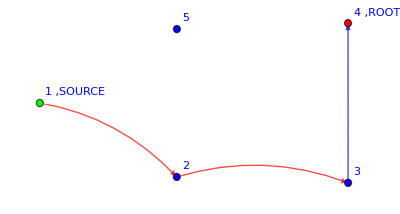

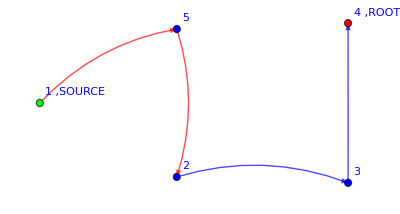

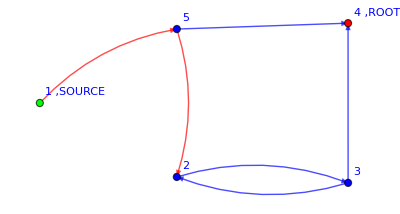

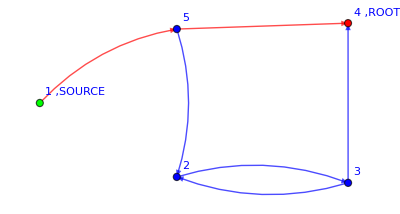

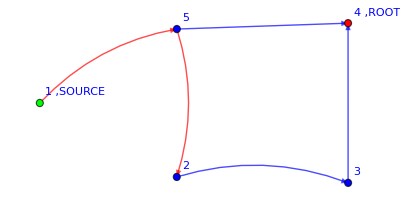

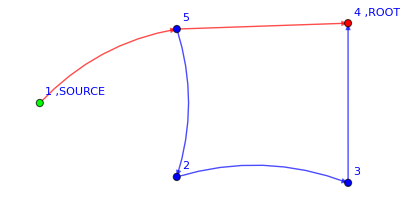

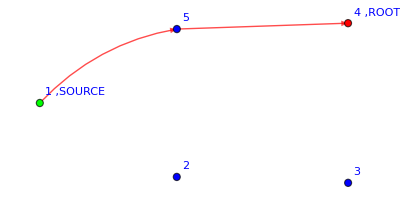

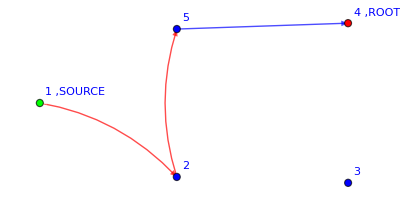

-Graphics-

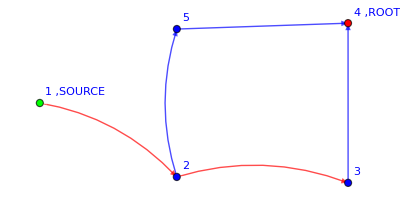

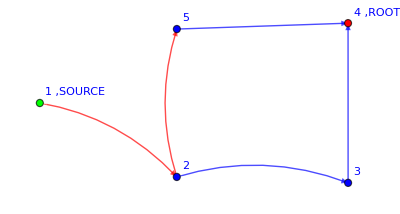

(β[1,2] β[2,3]^2 β[3,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2)+(β[1,5] β[2,3]^2 β[3,4]^2 β[5,2]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3]^2 β[3,2] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,5] β[2,3] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[5,4]^2)/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,2] β[2,5]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[2,3]^2 β[3,2]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3] β[3,2] β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,2] β[2,3] β[2,5] β[3,4] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))

```mathematica
g=myFavoriteGraph;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z Op[ϕs[1,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

## DynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[DynamicDLAaction];
Options[DynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{}};

DynamicDLAaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

###################  Partition Function  ##################

{{1},{-1/6,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{-1/6,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{-1/6,{1,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,2,RGBColor[0, 0, 1]},{2,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{1/36,{1,5,RGBColor[0, 0, 1]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,5,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{-1/9,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}}}

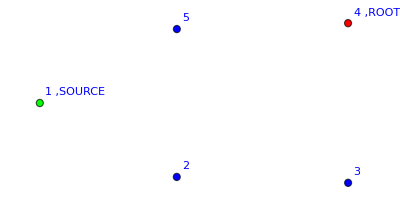

Weight==1

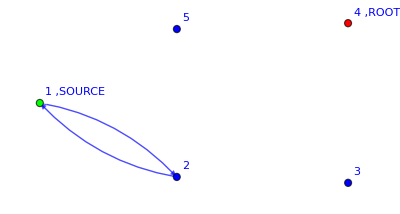

Weight==-1/6

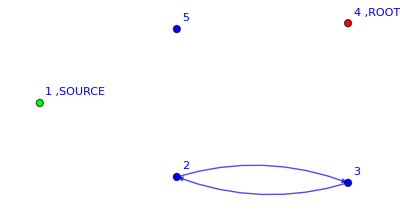

Weight==-1/6

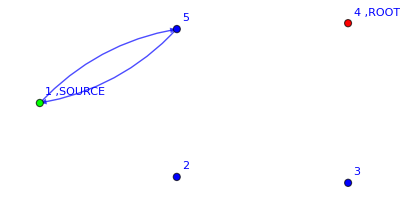

Weight==-1/6

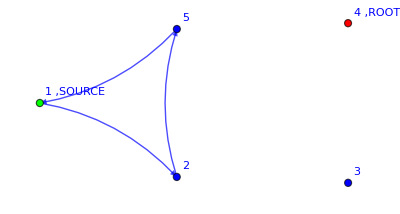

Weight==-1/18

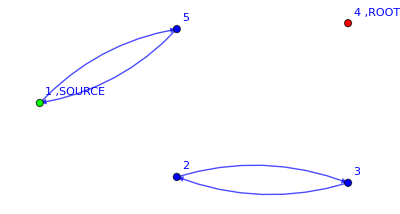

Weight==1/36

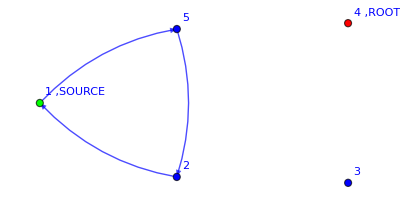

Weight==-1/18

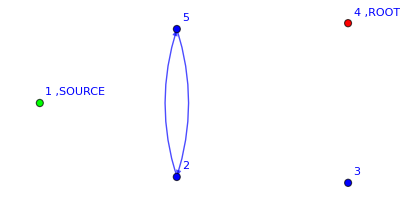

Weight==-1/9

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->True]
```

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

### Let’s check that kay’s trick for the total current works: IT WORKS ONLY FOR SYMMETRICAL β BUT WITH ANY σ!!!!!!

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]+
ExpectationValue[Z2  Op[χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]-

ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]+χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Operator found  ##################

###################  Operator found  ##################

0

```mathematica
(*Ok, I can insert the operators directly inside Op[]*)
```

Kay’s trick works only with symmetrical weights!!!!!

```mathematica
(*Now let's verify that kay's trick works*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z  ,"operator"->(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2,"operator"-> (β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

###################  Partition Function  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/(β_(2,5) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,4))+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))+β_(2,1) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z Op[(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2 Op[(β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

(β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Does it work for any σ? YESSS

```mathematica
g
```

-Graphics-

Exclude just 1: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
exp1=(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
exp2=(ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

σ/(σ+β_(4,3)+β_(4,5))-(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp2/.σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*A_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*B_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])->HoldForm[σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*(A+B+1)]
```

(σ (-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+1))/(σ+β_(4,3)+β_(4,5))

```mathematica
σ (exp1-exp2)
```

σ (1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-σ/(σ+β_(4,3)+β_(4,5))+(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
Limit[σ (exp1-exp2), σ -> ∞]-((-(Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))+(Subscript[β, 2,5] Subscript[β, 3,4] Subscript[β, 4,3] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 4,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,5] Subscript[β, 3,2] Subscript[β, 4,3] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 4,5] Subscript[β, 5,4])/((σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 4,5] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])))(σ+Subscript[β, 4,3]+Subscript[β, 4,5])+exp2(σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5]))^-1(Subscript[β, 4,3]+Subscript[β, 4,5]))//FullSimplify
```

0

```mathematica
(*CORRECT!!! THE LIMIT σ->∞ IS THE SAME AS THE BIG PARENTHESES. CHECK ONENOTE NOTEBOOK FOR DETAILS*)
```

```mathematica
Limit[σ(1-σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])),σ->∞]
```

β_(4,3)+β_(4,5)

```mathematica
Limit[σ((Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))),σ->∞]
```

(β_(3,4) β_(4,3))/(β_(3,2)+β_(3,4))

```mathematica
exp3=ExpectationValue[Z Op[β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(σ β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
σ(exp1-exp2)-exp3//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

(σ (β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Exclude 1 and 2: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1,2}];
exp1=σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

σ (1-σ/(σ+β_(4,3)+β_(4,5))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
exp2=ExpectationValue[Z Op[β[2,3]χs[3,Subscript[t, 1],1]+(β[1,5]+β[2,5])χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(2,3) β_(3,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp1-exp2//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

-(σ (β_(3,4) (β_(2,3)-β_(4,5))-β_(3,2) (β_(4,3)+β_(4,5))) (β_(5,1)+β_(5,2))+σ (β_(2,3) β_(3,4)+β_(1,5) (β_(3,2)+β_(3,4))+β_(2,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

### β or β/r? Answer: β!!

We want to check whether we need to use β or β/r in the DLA dynamical action

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp](*This is nicely normalized!!!*)
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{18/11},{-3/11,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{3/11,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{-2/11,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{6/11,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{2/11,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{-1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

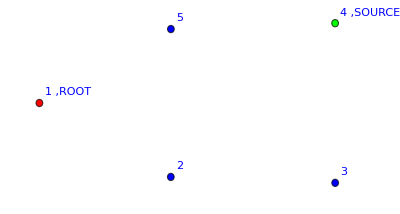

Weight==18/11

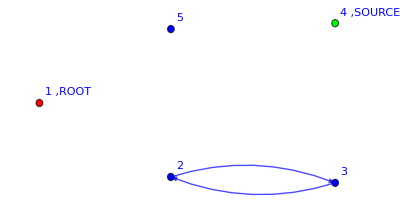

Weight==-3/11

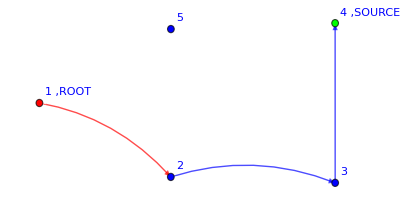

Weight==3/11

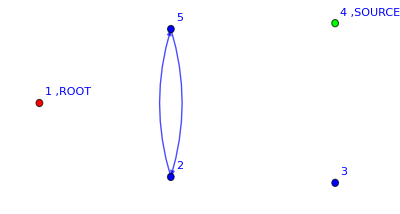

Weight==-2/11

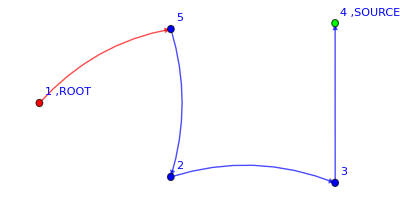

Weight==1/11

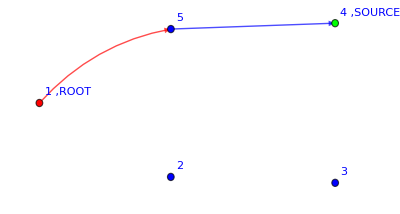

Weight==6/11

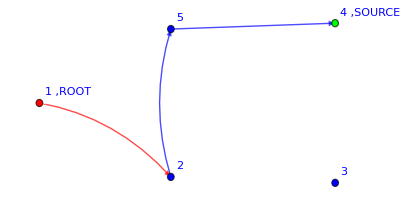

Weight==2/11

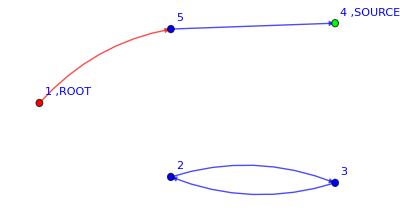

Weight==-1/11

```mathematica
DrawFromExpression[exp];
```

Now, if we use β/r: NOT PROPERLY NORMALIZED

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp]
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/12 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/18 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{(5 R_(1,2,RGBColor[1, 0, 0]))/22},{(3 R_(1,5,RGBColor[1, 0, 0]))/11}}

```mathematica
(*Not properly normalized!!!*)
```

### Can I send each field to zero immediately or do I need to do it at the end? Answer: YESSS!

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Partition function field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

V[1+χ_(4,1)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Ok, for the partition funciton it works. But in the partition function only χ is used*)
```

Observables: Op[ϕs[1,t_1,0]]

Right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False"Rrule"->{}]
```

###################  Operator found  ##################

V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]+R_(1,2,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,2) (χ^*)_(2,1)+R_(1,5,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,5) (χ^*)_(5,1)

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*OK!! IT SEEMS THAT I CAN DO FIRST A FIELD, SET TO ZERO, THEN THE OTHERS*)
```

## I would like to compute the denominator of the DLA transition probability. To do this, I try to use nn different fields and then send nn->-1.

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(1,t_2,k_1)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(2,t_2,k_2)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(3,t_2,k_3)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(4,t_2,k_4)] V[1+χ_(4,t_1,1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (χ^*)_(2,t_1,1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+R_(1,3,RGBColor[1, 0, 0]) β_(1,3) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (χ^*)_(3,t_1,1)+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) χ_(1,t_1,i_1) (χ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) (ϕ^*)_(1,t_2,k_2) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2) (χ^*)_(3,t_1,1)+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+R_(3,1,RGBColor[1, 0, 0]) β_(3,1) ϕ_(3,t_1,k_3) (ϕ^*)_(1,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(1,t_1,1)+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) χ_(3,t_1,i_3) (χ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) (ϕ^*)_(2,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_3) (χ^*)_(4,t_1,1)+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
ExpectationValue[Z Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])]Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

0

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2)^3 β_(2,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3)+(3 β_(1,2)^2 β_(2,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2)-(3 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,2)^3 β_(2,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,3)^2 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,3) β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(2,3)^3 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(2,3)^3 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,3)^3 β_(2,1)^3 β_(3,2)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,2)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,2)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(2,3)^3 β_(3,2)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2)^3 β_(2,1) β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,2)^2 β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^3 β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(2,1) β_(2,3)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,3)^2 β_(2,1)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^3 β_(2,1)^2 β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^3 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(2,1)^2 β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*SO, USING nn TIME-SLICES YIELDS Z^nn!!!! THIS IS EXPECTED. DOES IT WORK FOR <χ^*χ>?? *)
```

Does it work for <χ^*χ>?

###################  Operator found  ##################

{{1/12,{1,3,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{1/6,{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}}}

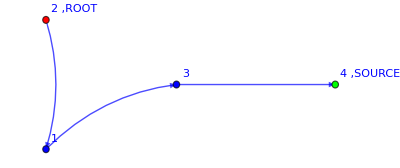

Weight==1/12

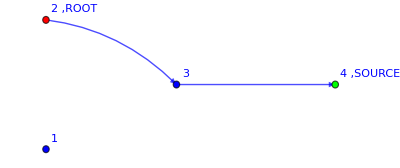

Weight==1/6

(β_(1,3) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->True,"graph"->g]
```

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]] Op[χs[2,Subscript[t, 2],1]] Op[χs[2,Subscript[t, 3],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

(β_(1,3)^3 β_(2,1)^3 β_(3,4)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,4)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(β_(2,3)^3 β_(3,4)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*IT WORKS!!!!!!!!!!!
CAN I USE THIS TO COMPUTE THE DENOMINATOR?????*)
```

Other attempt

```mathematica
Z=V[1+(Subscript[R, 1,2,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])+(Subscript[R, 1,3,RGBColor[0, 0, 1]] Subscript[β, 1,3] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])] V[1+(Subscript[R, 2,1,RGBColor[0, 0, 1]] Subscript[β, 2,1] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])+(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])] V[1+(Subscript[R, 3,1,RGBColor[0, 0, 1]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])];Z=Z/.χ[a_,b_,c_]->(ϕ[a,b,c])/.χs[a_,b_,c_]->ϕs[a,b,c]
```

V[1+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) ϕ_(1,t_1,i_1) (ϕ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) ϕ_(1,t_1,i_1) (ϕ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) ϕ_(2,t_1,i_2) (ϕ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) ϕ_(2,t_1,i_2) (ϕ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) ϕ_(3,t_1,i_3) (ϕ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) ϕ_(3,t_1,i_3) (ϕ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) ϕ_(3,t_1,i_3) (ϕ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
fields={χ,ϕ};
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]-(1-(Subscript[β, 1,2] Subscript[β, 2,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]))-(Subscript[β, 1,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,3] Subscript[β, 2,1] Subscript[β, 3,2])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])))^2//FullSimplify
```

###################  Partition Function  ##################

(2 β_(1,3)^2 β_(3,2) (-2 β_(2,3) (β_(2,1)+β_(2,3)) β_(3,1)-β_(2,1)^2 β_(3,2))-2 β_(1,2)^2 β_(2,3) (β_(2,3) β_(3,1)^2+2 β_(2,1) β_(3,2) (β_(3,1)+β_(3,2)+β_(3,4)))-4 β_(1,2) β_(1,3) β_(2,3) β_(3,2) (β_(2,3) β_(3,1)+β_(2,1) (3 β_(3,1)+β_(3,2)+β_(3,4))))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)

# Final Dynamical theories (?)

## FinalDynamicLERWaction[] BENCHMARK

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[FinalDynamicLERWaction];
Options[FinalDynamicLERWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

FinalDynamicLERWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=FinalDynamicLERWaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Observable ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1}];

expLERWbenchmark =ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand;
```

```mathematica
Replace[expLERWbenchmark,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1}]),1];

expLERWbenchmark2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
Replace[expLERWbenchmark2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1}]),1];

expLERWbenchmark3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
```

### ConvergenceLERW[] NO NORMALIZATION BY HAND

I want to check whether I really get the wrong result if I do not normalize at each step

```mathematica
Clear[ConvergenceLERW];
Options[ConvergenceLERW]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"gammaValue"->0.1};

ConvergenceLERW[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

Z=FinalDynamicLERWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;

locOperator= operator ;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision,i++,

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

#### Test ConvergenceLERW[]

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expLERW=ConvergenceLERW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3]
```

########## i=57, 9.20358×10^-16 ############

0.+9.20358×10^-16 ϕs[1,t_1,k_1]+3.97867×10^-8 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+7.29385×10^-15 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+1.16077×10^-7 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+7.73847×10^-8 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.108434 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+5.66125×10^-6 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.0000104152 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+5.66085×10^-6 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0722891 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0232245 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
expLERW1/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

expLERW1

```mathematica
expLERW1/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
```

expLERW1

```mathematica
(*THIS DOES NOT WORK: THE PROBABILITY IS NOT CONSERVED!!!*)
```

## LRWactionREALinteraction[] !!!!!!!!!!!!!! IT WORKS !!!!!!!!!!!!!! (BENCHMARK for only ψ excluded)

### LRWactionREALinteraction[]

The REAL interaction is not the one we wrote in the first place, nor the one with χ(x)-χ(y)! The real interaction is

```mathematica
γ β[x,y]((ϕs[y,t+1]χs[y,t] (*Diffusion solving the laplace equation *)
-ϕs[x,t+1]χs[x,t])ψs[x,t+1](*This is THE PROBABILITY TO STAY PUT, DO NOT DIFFUSE*)
-ϕs[x,t+1](χs[y,t] -χs[x,t])(*This keeps probability conserved*)
 )ϕ[x,t]
```

```mathematica
Clear[LRWactionREALinteraction];
Options[LRWactionREALinteraction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionREALinteraction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]]((R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]χs[y,Subscript[t, T],1]-ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[x,Subscript[t, T],1])ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]](χs[y,Subscript[t, T],1]-χs[x,Subscript[t, T],1])),{y,Length[locVertices]}]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]*χ[x,Subscript[t, T],Subscript[i, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
V[(1+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]])](*I AM SEPARATING ϕ and ψ!*)
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### Usage example of LRWactionREALinteraction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=LRWactionREALinteraction["graph"->g,"endTime"->endTime]/.β[__]->1;
```

Observable ϕs[1,t_1,k_1] WITHOUT PURIFICATION

```mathematica
Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}]
```

11/36

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}];

expLERWrealInteraction=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]+10/11 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
Replace[expLERWrealInteraction,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}]),1];

expLERWrealInteraction2=ExpectationValueBlock[Z % ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]+10/11 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+10/11 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-410/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+12/11 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+12/11 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-48/13 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+90/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+60/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+36/143 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+180/143 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

```mathematica
Replace[expLERWrealInteraction2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}]),1];

expLERWrealInteraction3=ExpectationValueBlock[Z % ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]-2 γ_3 ϕs[1,t_1,k_1]+4 γ_1 γ_3 ϕs[1,t_1,k_1]+4 γ_2 γ_3 ϕs[1,t_1,k_1]-8 γ_1 γ_2 γ_3 ϕs[1,t_1,k_1]+10/11 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+10/11 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-410/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+10/11 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-410/143 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-410/143 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+(12910 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/1859+12/11 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+12/11 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-48/13 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+12/11 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-48/13 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-48/13 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+(17616 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/1859+90/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+90/143 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+90/143 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-(4860 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/1859+60/143 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+60/143 γ_1 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+60/143 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]-(3240 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/1859+90/143 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+36/143 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+36/143 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+36/143 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-(9324 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5])/9295+180/143 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+180/143 γ_1 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+180/143 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]-720/169 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+108/715 γ_1 γ_2 γ_3 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+60/143 γ_1 γ_2 γ_3 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]

```mathematica
(*I need to check with the convergence*)
```

### ConvergenceLERWrealInteraction[]

```mathematica
Clear[ConvergenceLERWrealInteraction];
Options[ConvergenceLERWrealInteraction]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceLERWrealInteraction[operator_,OptionsPattern[]]:=Module[{Z,Z0,locOperator,locPrecision,locγ,exp,i=1,temp},

Z=LRWactionREALinteraction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;

locOperator= operator/Znorm[operator,"graph"->OptionValue["graph"],"fieldsToExclude"->{ψs}]; (*Normalized immediately*)
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"],"nχ"->-1];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*LOOP*)
For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fieldsToExclude"->{ψs}]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"],"nχ"->-1];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

#### Test ConvergenceLERWrealInteraction[]

My favorite graph

```mathematica
g=myFavoriteGraph;
precision=10^-30;
expLERWconvREALinteraction=ConvergenceLERWrealInteraction[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.15];
```

########## i=195, 8.89242×10^-31 ############

```mathematica
expLERWconvREALinteraction
```

0.+8.89242×10^-31 ϕs[1,t_1,k_1]+1.04566×10^-16 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+4.30579×10^-20 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+8.2532×10^-14 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+5.50213×10^-14 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+2.59544×10^-9 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+3.89315×10^-9 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
expLERWconvREALinteraction/.ϕs[__]->1/.ψs[__]->1/.ξs[__]->0/.R[__]->1
```

1.

```mathematica
expLERWconvREALinteraction/.a_/;Abs[a]<10^-5:>0/.ϕs[__]->1/.ψs[__]->1/.ξs[__]->0
Rationalize[%,0.0001]
```

0.272727 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0909091 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.454545 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.181818 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/11 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/11 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+5/11 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+2/11 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

```mathematica
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!CORRECT!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
```

## LRWactionγNormalizedNextTime[] NOT CORRECT

### LRWactionγNormalizedNextTime[]

V19 : I want to check whether I can change the normalization of γ by evaluating χ_1^1 on the next time step

```mathematica
Clear[LRWactionγNormalizedNextTime];
Options[LRWactionγNormalizedNextTime]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

LRWactionγNormalizedNextTime[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]χs[y,Subscript[t, T+1],1]χ[locSource,Subscript[t, T+1],1]-ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[x,Subscript[t, T],1]),{y,Length[locVertices]}]*ϕ[x,Subscript[t, T],Subscript[k, x]])](* I ALWAYS NEED THE TARGET AT THE NEXT STEP*)
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]*χ[x,Subscript[t, T],Subscript[i, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
V[(1+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]])](*I AM SEPARATING ϕ and ψ!*)
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### Usage example of LRWactionγNormalizedNextTime[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
g=myFavoriteGraph;
endTime=1;
Z=LRWactionγNormalizedNextTime["graph"->g,"endTime"->endTime]/.β[__]->1;
```

Observable ϕs[1,t_1,k_1]

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}];

expLERWγNormalizedNextTime=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]+γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[2,t_1,1] ψs[1,t_1,ll_1]+γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[5,t_1,1] ψs[1,t_1,ll_1]

```mathematica
Replace[expLERWγNormalizedNextTime,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"βrule"->{β[__]->1},"fieldsToExclude"->{ψs}]),1];

ExpectationValueBlock[Z % ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand
%/.χs[_,Subscript[t, 1],1]->0
```

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[2,t_1,1] ψs[1,t_1,ll_1]-2 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[2,t_1,1] ψs[1,t_1,ll_1]+γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[5,t_1,1] ψs[1,t_1,ll_1]-2 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[5,t_1,1] ψs[1,t_1,ll_1]+5/13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] χs[1,t_1,1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+5/13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] χs[3,t_1,1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+5/13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] χs[5,t_1,1] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+6/13 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_1,k_1] χs[1,t_1,1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+6/13 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] χs[2,t_1,1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+6/13 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] χs[4,t_1,1] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

ϕs[1,t_1,k_1]-2 γ_1 ϕs[1,t_1,k_1]-2 γ_2 ϕs[1,t_1,k_1]+4 γ_1 γ_2 ϕs[1,t_1,k_1]+5/13 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+6/13 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

### ConvergenceLERWγNormalizedNextTime[]

```mathematica
Clear[ConvergenceLERWγNormalizedNextTime];
Options[ConvergenceLERWγNormalizedNextTime]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceLERWγNormalizedNextTime[operator_,OptionsPattern[]]:=Module[{Z,Z0,locOperator,locPrecision,locγ,exp,i=1,temp},

Z=LRWactionγNormalizedNextTime["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;

locOperator= operator/Znorm[operator,"graph"->OptionValue["graph"],"fieldsToExclude"->{ψs}]; (*Normalized immediately*)
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"],"nχ"->-1];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*LOOP*)
For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fieldsToExclude"->{ψs}]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"],"nχ"->-1];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];


exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fieldsToExclude"->{ψs}]),1];

exp=ExpectationValueBlock[(Z/.γ->0) exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"],"nχ"->-1];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

Return[exp];
]
```

#### Test ConvergenceLERWγNormalizedNextTime[]

My favorite graph

```mathematica
g=myFavoriteGraph;
precision=10^-10;
expLERWconvγNormalizedNextTime=ConvergenceLERWγNormalizedNextTime[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->200,"precision"->precision,"gammaValue"->0.15];
```

########## i=66, 8.53832×10^-11 ############

```mathematica
expLERWconvγNormalizedNextTime
```

0.+8.53832×10^-11 ϕs[1,t_1,k_1]+2.37321×10^-6 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+2.53587×10^-7 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+0.0000366188 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.0000244125 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.112382 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+0.00024675 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.201282 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.000346946 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0749214 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.0414647 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
expLERWconvγNormalizedNextTime/.ϕs[__]->1/.ψs[__]->1/.ξs[__]->0/.R[__]->1
```

0.430707

```mathematica
temp=ConvergenceLERWγNormalizedNextTime[expLERWconvγNormalizedNextTime,"graph"->g,"steps"->200,"precision"->precision*10^-5,"gammaValue"->0.15];
```

########## i=33, 9.42996×10^-16 ############

```mathematica
temp
```

0.+9.42996×10^-16 ϕs[1,t_1,k_1]+1.28175×10^-8 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+3.48633×10^-10 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+7.29757×10^-7 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+4.86505×10^-7 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+0.367918 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3]+0.0000329167 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.548951 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]+0.0000487296 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.245278 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[5,t_1,ll_5]+0.137402 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2] ψs[3,t_1,ll_3] ψs[5,t_1,ll_5]

```mathematica
temp/.ϕs[__]->1/.ψs[__]->1/.ξs[__]->0/.R[__]->1
```

1.29963

```mathematica
expLERWconvγNormalizedNextTime/.a_/;Abs[a]<10^-4:>0/.ϕs[__]->1/.ψs[__]->1/.ξs[__]->0
Rationalize[%,0.0001]
```

0.112382 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.00024675 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.000346946 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.0414647 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.201282 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.0749214 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

10/89 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+(R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]])/4052+(R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]])/2882+6/145 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+30/149 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+3/40 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

```mathematica
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!CORRECT!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
```